# Fitting NMR Signal

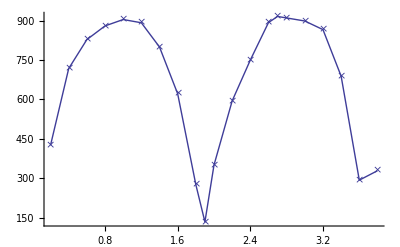

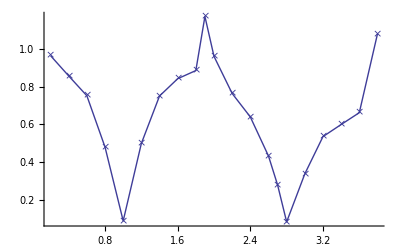

```mathematica
K={
{0.2,425.8},
{0.4,717.8},
{0.6,828.0},
{0.8,880.1},
{1.0,904.4},
{1.2,892.1},
{1.4,799.7},
{1.6,621.6},
{1.8,275.7},
{1.9,133.8},
{2.0,350.3},
{2.2,594.5},
{2.4,750.1},
{2.6,892.9},
{2.7,916.1},
{2.8,910.4},
{3.0,898.8},
{3.2,866.0},
{3.4,688.7},
{3.6,292.8},
{3.8,328.6}};
R={
{0.2,410.5/425.8},
{0.4,614.8/717.8},
{0.6,622.1/828.0},
{0.8,421.7/880.1},
{1.0,79.4/904.4},
{1.2,444.5/892.1},
{1.4,599.8/799.7},
{1.6,523.2/621.6},
{1.8,244.0/275.7},
{1.9,156.8/133.8},
{2.0,336.4/350.3},
{2.2,453.9/594.5},
{2.4,479.3/750.1},
{2.6,385.6/892.9},
{2.7,255.3/916.1},
{2.8,75.0/910.4},
{3.0,302.9/898.8},
{3.2,463.1/866.0},
{3.4,412.4/688.7},
{3.6,193.7/292.8},
{3.8,354.6/328.6}};
G=ListPlot[{K},PlotRange->{{0,4},{0,All}},Joined->True,PlotMarkers->{ {"×",Large}}]
H=ListPlot[{R},PlotRange->{{0,4},{0,All}},Joined->True,PlotMarkers->{ {"×",Large}}]
```

```mathematica
J=NonlinearModelFit[K,A √(((-1+Cos[1.682α])^2 Cos[θ]^2+Sin[1.682 α]^2) Sin[θ]^2),{A,θ},α];
Normal[J]
Manipulate[Show[
Plot[{Normal[J]},{α,0,4},PlotStyle->{Red}],G,Plot[A √(((-1+Cos[k  α])^2 Cos[θ °]^2+Sin[k α]^2) Sin[θ °]^2),{α,0,4},PlotStyle->Green]],{{A,875},850,900},{{θ,80},60,90},{{k,1.656},1.5,3}]
```

983.955 √(0.0137606 (-1+Cos[1.682 α])^2+Sin[1.682 α]^2)

```mathematica
Solve[Cos[θ °]^2==0.013760631019554005   ,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-96.7366},{θ→-83.2634},{θ→83.2634},{θ→96.7366}}

```mathematica
S=NonlinearModelFit[R,Abs[√(Cos[θ ]^2+Cos[1.682α ] Sin[θ ]^2)],{θ},α];
Normal[S]
Manipulate[Show[
Plot[{Normal[S]},{α,0,4},PlotStyle->{Red}],H,Plot[Abs[√(Cos[θ °]^2+Cos[k α ] Sin[θ ° ]^2)],{α,0,4},PlotStyle->Green]],{{θ,83.1},60,90},{{k,1.6},1.2,3}]
```

√Abs[0.0736486+0.926351 Cos[1.682 α]]

```mathematica
Solve[Sin[θ °]^2==0.8942250535588715 ,θ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→-71.0205},{θ→71.0205}}